### PARAMETRES

```mathematica
ClearAll;
```

```mathematica
listH ={50,100,200}; (*мощности слоев*)
slopes = {0Degree, 0.5 Degree, 0 Degree, 0 Degree} ;(*наклон слоев*)

len = 10000;(*длина профиля*)
dx = 100;(*шаг по профилю*)

type = -1 ;
```

```mathematica
(*folding parametres *)
maxFoldThickness = 1000;(*степень складчатости нижнего слоя в метрах*)
foldingParameters = {3,5}; (*степень влияния нижнего горизонта на верхние*)
```

```mathematica
listV = {1500,2200,2500,2700, 2900, 3000,3100}; 
velocityTrend = {4,3,2,1.5,1.2,1,1};(*1 or 0*)
velocityAnomaly ={0,0,0,0,0,0,0}; (*1 or 0*)
```

```mathematica
wellCount= 10 ;(*кол скважин*)
wellType = "max"; (*расположение скважин "max","min","regular","random"*)
```

### DEPTH

```mathematica
depthModel = DepthSection[listH, slopes, len, dx, type, maxFoldThickness, foldingParameters][["horizons"]];
(*table = DepthSection[listH, slopes, len, dx, type, maxFoldThickness, foldingParameters][["table"]];*)
```

```mathematica
optsDepth = {Filling -> Bottom, Frame -> True, ImageSize -> 400,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[depthModel]] - 1)],
						PlotLabel -> "Глубинный разрез",FrameLabel->{"x, м","z, м"}, AspectRatio->1.1};
PlotDepthSection[depthModel, optsDepth]
```

-Graphics-

```mathematica
(*Show[ListLinePlot[Table[{time[[i, j, 1]], -time[[i, j, 2]]}, {i, Length[time]}, {j, Length[time[[i]]]}], optsDepth],
			ListLinePlot[Table[{time[[i, j, 1]], -time[[i, j, 2]]}, {i, Length[time]}, {j, Length[time[[i]]]}], {PlotStyle -> {Directive[Thickness[0.004], Black]}, PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],ImageSize -> 500}], {Frame -> True,
			FrameStyle -> Directive[14, Black], FrameLabel->{"x, м","z, м"},
			PlotRangePadding -> {{Scaled[0.05], Scaled[0.2]}, {Scaled[0.05], Scaled[0.05]}}}
] *)
```

### VELOCITY

```mathematica
(*timeReverse = Table[{time[[i, j, 1]], -time[[i, j, 2]]*1000}, {i, Length[time]}, {j, Length[time[[i]]]}];*)
```

```mathematica
velModel=VelocitySection[depthModel,listV, velocityTrend, velocityAnomaly][["model"]];
```

```mathematica
PlotVelocity[velModel, horizons]
```

```mathematica
dsVelModel=VelocitySection[depthModel,listV, velocityTrend, velocityAnomaly][["ds"]];
```

### TIME

```mathematica
timeModel=TimeSection[depthModel, velModel][["time"]];
optsTime = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t" <> ToString[#] &, (Range[Length[timeModel]] - 1)],
						PlotLabel -> "Временной разрез", AspectRatio->1.1, FrameLabel-> {"x, м", "t, с"}};PlotTimeSection[timeModel, optsTime]
```

-Graphics-

### WELLS

```mathematica
dsWells= WellSet[depthModel, timeModel, wellCount, wellType][["ds"]]
positionsWells = WellSet[depthModel, timeModel,  wellCount, wellType][["positions"]]
PlotDepthSection[depthModel, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
							PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[depthModel]] - 1)],
						GridLines->{DeleteDuplicates[Normal[dsWells[All, "x"]]], None},GridLinesStyle->Directive[RGBColor["#405591"],Dashed,Thick],											
											PlotLabel -> "Глубинный разрез со скважинами"}, AspectRatio->1.1, FrameLabel-> {"x, м", "h, м"}]
```

{700,2600,3800,5100,6300,7500,9000}

-Graphics-

#### !!! неправильно считает. позиция = 7, а ее икс = 600

```mathematica
PlotTimeSection[timeModel, {GridLines->{DeleteDuplicates[Normal[dsWells[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[timeModel]] - 1)],
						PlotLabel -> "Временной разрез со скважинами"
}]
```

-Graphics-

### CheckVelocity

```mathematica
dsVint= CheckVelocity[dsWells][["ds"]]
```

### HTMethod

```mathematica
Clear[t];
lmSetHT=HTMethod2D[dsWells,timeModel, t][["lmSet"]]
lmParametresHT=HTMethod2D[dsWells,timeModel, t][["lmParametres"]];

dObjHT=HTMethod2D[dsWells,timeModel, t][["depthObjective"]];
dPredHT=HTMethod2D[dsWells,timeModel, t][["depthPredicted"]];

resultHT=HTMethod2D[dsWells,timeModel, t][["result"]];
wellValuesHT=HTMethod2D[dsWells,timeModel, t][["wellValues"]];
fitsHT = HTMethod2D[dsWells,timeModel, t][["fits"]];

RSquaredHT=HTMethod2D[dsWells,timeModel, t][["RSquared"]]
```

{FittedModel[17.0063+2578.91 t],FittedModel[111.635+2456.77 t],FittedModel[271.087+2280.89 t],FittedModel[734.238+1811.28 t]}

{0.999512,0.998624,0.98882,0.852991}

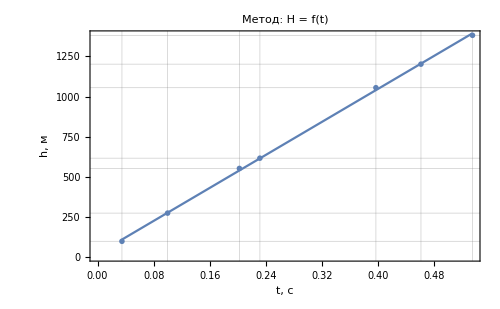
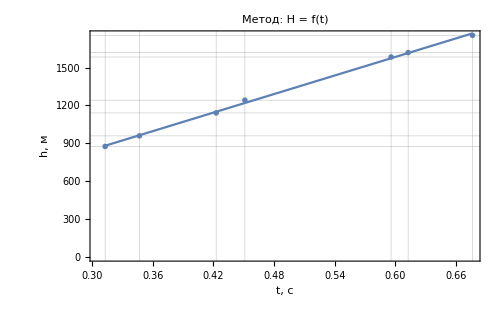
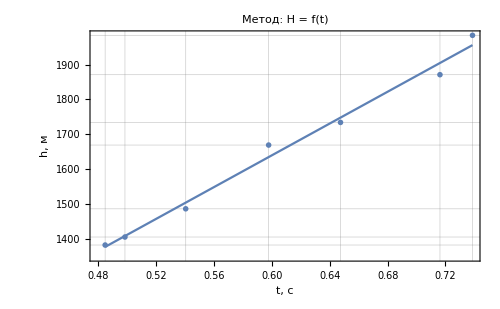
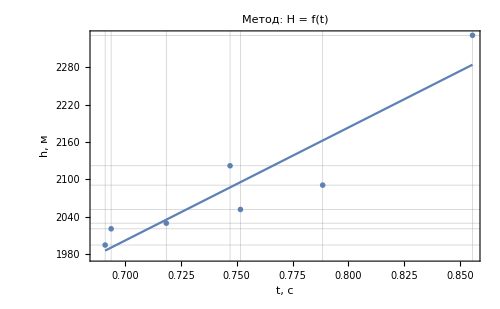

```mathematica
LinearRegressionPlots[wellValuesHT[[All,All, 2;;3]],lmSetHT, t, "H = f(t)", {"t, с","h, м"}]
```

### VTMethod

```mathematica
lmSetVT=VTMethod2D[dsWells,timeModel, t][["lmSet"]]
lmParametresVT=VTMethod2D[dsWells,timeModel, t][["lmParametres"]];

dObjVT=VTMethod2D[dsWells,timeModel, t][["depthObjective"]];
dPredVT=VTMethod2D[dsWells,timeModel, t][["depthPredicted"]];

resultVT = VTMethod2D[dsWells,timeModel, t][["result"]];
wellValuesVT=VTMethod2D[dsWells,timeModel, t][["wellValues"]];
fitsVT = VTMethod2D[dsWells,timeModel, t][["fits"]];

RSquaredVT=VTMethod2D[dsWells,timeModel, t][["RSquared"]]
```

{FittedModel[2764.93-322.809 t],FittedModel[2940.63-488.014 t],FittedModel[3196.22-754.044 t],FittedModel[3764.6-1292.44 t]}

{0.90184,0.912837,0.79522,0.615102}

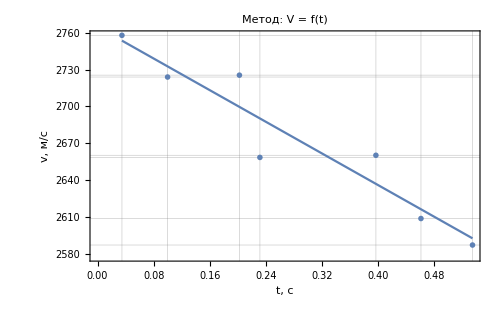
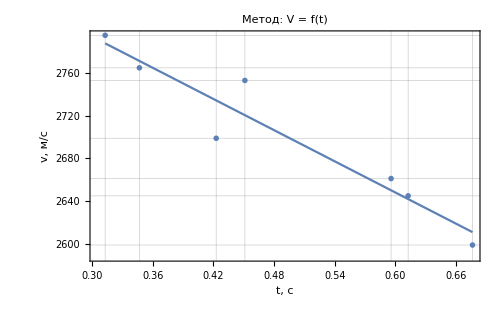
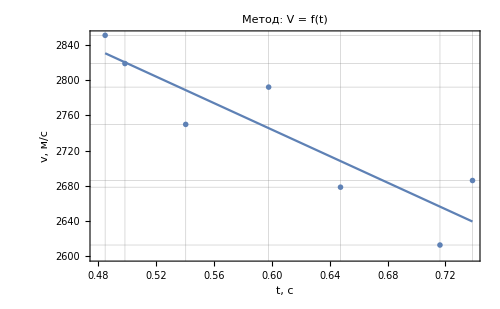
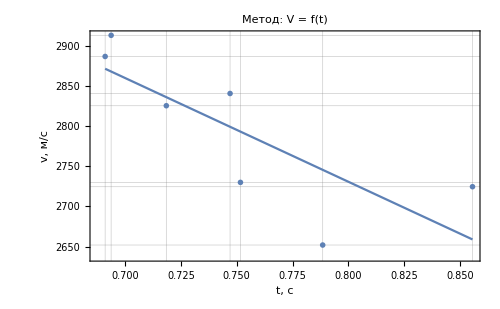

```mathematica
LinearRegressionPlots[wellValuesVT[[All, All,2;;3]],lmSetVT, t, "V = f(t)", {"t, с","v, м/с"}]
```

### THMethod

```mathematica
Clear[h];
lmSetTH=THMethod2D[dsWells,timeModel, h][["lmSet"]]
lmParametresTH=THMethod2D[dsWells,timeModel, h][["lmParametres"]]

dObjTH=THMethod2D[dsWells,timeModel,h][["depthObjective"]];
dPredTH=THMethod2D[dsWells,timeModel, h][["depthPredicted"]];

resultTH=THMethod2D[dsWells,timeModel, h][["result"]];
wellValuesTH = THMethod2D[dsWells,timeModel, h][["wellValues"]];
fitsTH = THMethod2D[dsWells,timeModel, h][["fits"]];

RSquaredTH=THMethod2D[dsWells,timeModel, h][["RSquared"]]
```

{FittedModel[-0.00645461+0.000387571 h],FittedModel[-0.0447055+0.000406478 h],FittedModel[-0.110777+0.000433524 h],FittedModel[-0.235599+0.000470932 h]}

{{-0.00645461,0.000387571},{-0.0447055,0.000406478},{-0.110777,0.000433524},{-0.235599,0.000470932}}

{0.999512,0.998624,0.98882,0.852991}

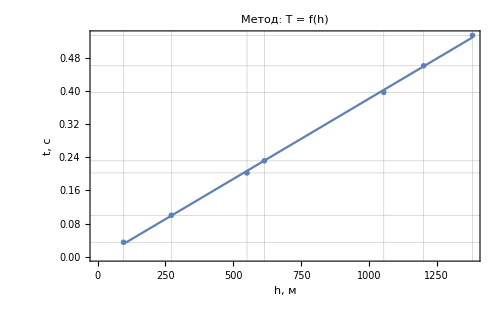
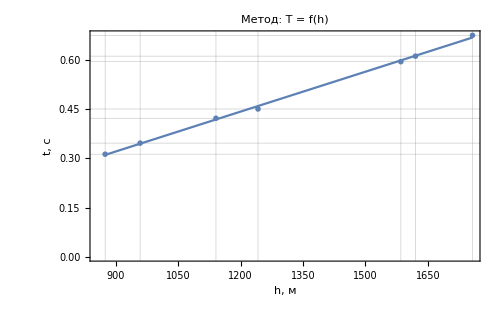
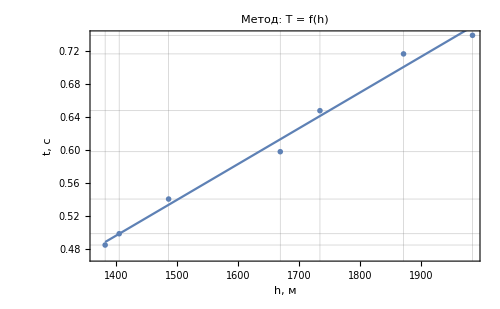
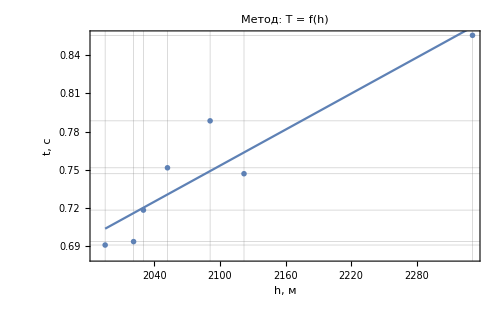

```mathematica
LinearRegressionPlots[wellValuesTH[[All, All,2;;3]],lmSetTH, h, "T = f(h)", {"h, м","t, с"}]
```

```mathematica
(*TimesBy[wellValuesTH[[All,All,2]],1000]
```

### VaveMethod

```mathematica
vAveTable=VaveMethod2D[dsWells,timeModel][["vAveTable"]]
resultVave=VaveMethod2D[dsWells,timeModel][["result"]];
fitsVave = VaveMethod2D[dsWells,timeModel][["fits"]];
```

{2674.56,2702.33,2741.26,2795.97}

```mathematica
dsWells
```

```mathematica
DeleteDuplicates[Normal[dsWells[All, "x"]]]
```

{600,2500,3700,5000,6200,7400,8900}

### VaveRegressionMethod2D

```mathematica
Length[timeModel]
```

5

```mathematica
timeModel[[1]]
```

{{0,0},{100,0},{200,0},{300,0},{400,0},{500,0},{600,0},{700,0},{800,0},{900,0},{1000,0},{1100,0},{1200,0},{1300,0},{1400,0},{1500,0},{1600,0},{1700,0},{1800,0},{1900,0},{2000,0},{2100,0},{2200,0},{2300,0},{2400,0},{2500,0},{2600,0},{2700,0},{2800,0},{2900,0},{3000,0},{3100,0},{3200,0},{3300,0},{3400,0},{3500,0},{3600,0},{3700,0},{3800,0},{3900,0},{4000,0},{4100,0},{4200,0},{4300,0},{4400,0},{4500,0},{4600,0},{4700,0},{4800,0},{4900,0},{5000,0},{5100,0},{5200,0},{5300,0},{5400,0},{5500,0},{5600,0},{5700,0},{5800,0},{5900,0},{6000,0},{6100,0},{6200,0},{6300,0},{6400,0},{6500,0},{6600,0},{6700,0},{6800,0},{6900,0},{7000,0},{7100,0},{7200,0},{7300,0},{7400,0},{7500,0},{7600,0},{7700,0},{7800,0},{7900,0},{8000,0},{8100,0},{8200,0},{8300,0},{8400,0},{8500,0},{8600,0},{8700,0},{8800,0},{8900,0},{9000,0},{9100,0},{9200,0},{9300,0},{9400,0},{9500,0},{9600,0},{9700,0},{9800,0},{9900,0},{10000,0}}

```mathematica
(* метод нормализует средние скорости на скорости ОГТ. Нужны скорости ОГТ, т.к. это модельные данные, их нет. Сейчас скорости ОГТ расчитываются внутри самого модуля VaveRegressionMethod2D как vOGTTable = RandomReal[{0.5, 1.5}] * #&/@vAveTable;*)


vAveTable = Extract[#, Partition[DeleteDuplicates[Normal[dsWells[All, "x"]]]/dx, 1]]&/@(Table[Table[Abs[(depthModel[[i, j, 2]] - depthModel[[1, j, 2]]) / 2/timeModel[[i, j, 2]]], {j, Length[depthModel[[i]]]}], {i, 2, Length[depthModel]}])
vOGTTable = RandomReal[{0.5, 1.5}] * #&/@vAveTable
(*считаем снаружи модуля иначе скорости будут ересчитываться при каждом вызове*)


Clear[v];
lmSetVaveVOGT=VaveRegressionMethod2D[dsWells, depthModel, timeModel, vOGTTable, v][["lmSet"]]
lmParametresVaveVOGT=VaveRegressionMethod2D[dsWells, depthModel, timeModel,vOGTTable, v][["lmParametres"]];

dObjVaveVOGT=VaveRegressionMethod2D[dsWells, depthModel, timeModel,vOGTTable,  v][["depthObjective"]]
dPredVaveVOGT=VaveRegressionMethod2D[dsWells, depthModel, timeModel, vOGTTable, v][["depthPredicted"]]

resultVaveVOGT=VaveRegressionMethod2D[dsWells, depthModel, timeModel,vOGTTable, v][["result"]];
wellValuesVaveVOGT= VaveRegressionMethod2D[dsWells, depthModel, timeModel,vOGTTable, v][["wellValues"]];
fitsVaveVOGT = VaveRegressionMethod2D[dsWells, depthModel, timeModel, vOGTTable,v][["fits"]];

RSquaredVaveVOGT=VaveRegressionMethod2D[dsWells, depthModel, timeModel, vOGTTable, v][["RSquared"]]

plotDataVaveVOGT=VaveRegressionMethod2D[dsWells, depthModel, timeModel,vOGTTable, v][["plotData"]];

errors=VaveRegressionMethod2D[dsWells, depthModel, timeModel,vOGTTable, v][["errors"]]
```

{{654.1,665.485,674.747,639.368,679.95,660.394,680.717},{662.747,674.521,688.765,643.045,687.08,662.202,694.505},{672.566,686.314,703.881,646.779,696.815,666.944,709.416},{681.795,704.224,721.891,657.182,708.854,680.271,725.913}}

{{821.923,836.23,847.868,803.412,854.406,829.832,855.37},{860.377,875.662,894.153,834.8,891.967,859.67,901.605},{919.784,938.585,962.61,884.518,952.947,912.095,970.179},{920.778,951.069,974.929,887.537,957.322,918.719,980.36}}

{FittedModel[-1.82514×10^-10+0.795816 v],FittedModel[-3.3351×10^-10+0.770298 v],FittedModel[2.88198×10^-11+0.731222 v],FittedModel[5.87507×10^-11+0.740455 v]}

{{-1202.,-615.001,-272.001,-1382.,-551.001,-1055.,-96.0015},{-1620.,-1141.,-959.001,-1757.,-1242.,-1585.,-875.001},{-1984.,-1486.,-1405.,-1871.,-1669.,-1734.,-1382.},{-2331.,-2030.,-1995.,-2091.,-2122.,-2052.,-2021.}}

{{-239.143,-122.357,-54.1158,-274.955,-109.624,-209.897,-19.0999},{-311.971,-219.728,-184.679,-338.354,-239.178,-305.231,-168.503},{-362.686,-271.649,-256.842,-342.029,-305.103,-316.985,-252.637},{-431.501,-375.781,-369.302,-387.073,-392.812,-379.854,-374.115}}

{1.,1.,1.,1.}

{{-962.858,-492.644,-217.886,-1107.05,-441.378,-845.105,-76.9016},{-1308.03,-921.274,-774.322,-1418.65,-1002.82,-1279.77,-706.498},{-1621.32,-1214.35,-1148.16,-1528.97,-1363.9,-1417.02,-1129.36},{-1899.5,-1654.22,-1625.7,-1703.93,-1729.19,-1672.15,-1646.89}}

```mathematica
фигня фигней
```

```mathematica
(*ListPlot[plotDataVaveVOGT]*)
```

### GRAPHICS

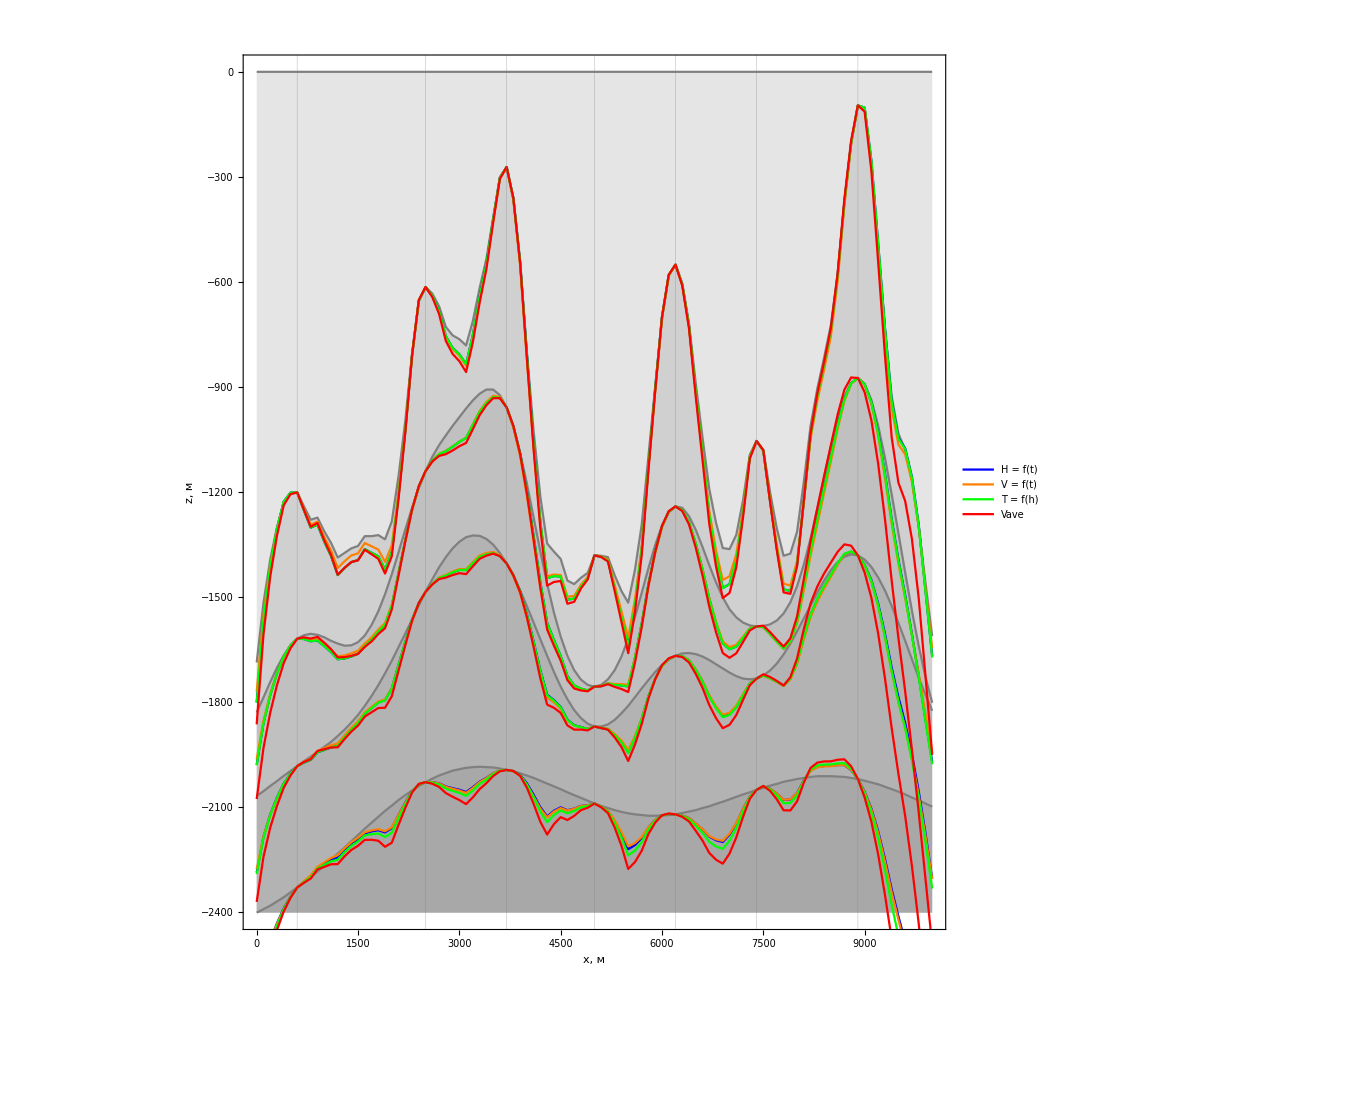

```mathematica
opts1 = {GridLines->{DeleteDuplicates[Normal[dsWells[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000, FrameLabel->{"x, м", "z, м"},FrameStyle->Directive[16, Black], LabelStyle->Directive[16, Black], 
					PlotLabels -> Placed[Map["" <> ToString[#] &, (Range[Length[horizons]] - 1)], {After}],PlotStyle->Gray, AspectRatio->1.1};
opts2= {PlotStyle->{Blue},PlotLegends->{"H = f(t)"}};
opts3 = {PlotStyle->{Orange}, PlotLegends->{"V = f(t)"}};
opts4 = {PlotStyle->{Green}, PlotLegends->{"T = f(h)"}};
opts5 = { PlotStyle->{Red}, PlotLegends->{"Vave"}};
allHorizons = {depthModel,resultHT, resultVT, resultTH, resultVave};
opts = {opts1, opts2,opts3, opts4, opts5};
PlotPredictionModel2D[wellDataset, allHorizons, opts]
```

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[dsWells[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[dsWells]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[dsWells[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[dsWells]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultTH,  GridLines->{DeleteDuplicates[Normal[dsWells[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[dsWells]] - 1)],
						PlotLabel -> "T(H)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVave,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVaveVOGT,  GridLines->{DeleteDuplicates[Normal[dsWells[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[dsWells]] - 1)],
						PlotLabel -> "Vave = f(vOGT)"]
```

-Graphics-